```mathematica
Nt = 20; 
ti = 0; tf = 5; 
deltat = (tf - ti) /Nt ;
Nx = 20;
xi = -40; xf = 40; 
deltax = (xf - xi) / Nx; 
c =  1;

(*For Max Eigenvalue Plots*)
rs = Table[0.1*i,{i,1,200}];

maxevalsLD2 = Table[0,{i,1,Length[rs]}];
maxevalsRK2 = Table[0,{i,1,Length[rs]}];
maxevalsPI = Table[0,{i,1,Length[rs]}];



Subscript[δ, i_,j_]:=KroneckerDelta[i,j];

selectwidth = 5;
diffOrder = 2;
deriv = 2;


(*The total number of points in the stencil*)
totalpoints = (2*selectwidth) + 1;

(*The middle point in the stencil*)
middlepoint = selectwidth + 1;

(*Set up the grid for the stencil*)
grid=x0+(Range[totalpoints]-middlepoint)Δx;

(LP=NDSolve`FiniteDifferenceDerivative[Derivative[deriv],grid,"DifferenceOrder"->diffOrder]@"DifferentiationMatrix"//Normal);

(*define r:=Δt/(Δx^deriv)*)
r=.;
LPX = LP*((-1)^deriv)*(r*(Δx)^deriv);

gn = (LPX[[middlepoint,All]]//Normal)//Simplify//FullSimplify;
LPX = Table[RotateRight[gn,i],{i,-selectwidth,selectwidth}];

IP=IdentityMatrix[Length[LPX]];

(Mn=Inverse[IP-(ⅈ * LPX)/4 ].(IP+(ⅈ * LPX)/4));

fn=(Mn[[middlepoint,All]]//Normal)//Simplify//FullSimplify;

(*Generate a M Matrix from the L matrix for the stencil*)
MP = Table[0,{i,1,Nx},{j,1,Nx}];

(*WITH Periodic Boundary Conditions*)
MP = Table[Sum[(Subscript[δ, i,j+(middlepoint-k)])fn[[k]] + (Subscript[δ, i,(j-k)])fn[[middlepoint + k]],{k,selectwidth}] + Subscript[δ, i,j] fn[[middlepoint]] + Sum[(Subscript[δ, (i + Nx) - n,j])fn[[selectwidth - n]] + (Subscript[δ, (i + Nx) + n,(j + 2*Nx)])fn[[(middlepoint + 1) + n]]  ,{n,0,selectwidth - 1}],{i,0,Nx-1},{j,0,Nx-1}];
```

```mathematica
Do[
deltat = (deltax^2) * rs[[p]];

Xp= N[Table[xm = xi + m *deltax, {m, 0, Nx}],32];

T = N[Table[tn = ti + n *deltat, {n, 0, Nt -1 }],32];
Xo = N[Table[xn = xi + n *deltax, {n, 0, Nx -1}],32];

f[x_] = ⅇ^(- x^2+ⅈ x);


(************************************************************************************************************************)
(*Differentiation Matrix*)
(************************************************************************************************************************)
L1 = N[(NDSolve`FiniteDifferenceDerivative[Derivative[1],Xp,"DifferenceOrder"->1, PeriodicInterpolation->True]@"DifferentiationMatrix"//Normal),32];
L1//MatrixForm;
DL1 = N[-c * L1 * deltat,32];

L2 = N[Table[(NDSolve`FiniteDifferenceDerivative[Derivative[i],Xp, "DifferenceOrder"->2, PeriodicInterpolation->True]@"DifferentiationMatrix"//Normal), {i,1,8}],32];
DL2 = L2[[2]] * deltat * (ⅈ / 2);


(* LD2 *)
ILD2 = N[IdentityMatrix[Length[DL2]],32];
ALD2 = N[ILD2 - (DL2 / 2),32];
BLD2 = N[ILD2 + (DL2 / 2),32];
MLD2 = N[Inverse[ALD2].BLD2,32];

evals = Eigenvalues[N[MLD2]];

maxevalsLD2[[p]] = Max[Abs[evals]];

(*PI*)

MPtest = N[MP//.{r -> (deltat / (deltax)^deriv)},32];

evalsPI = Eigenvalues[N[MPtest]];

maxevalsPI[[p]] = Max[Abs[evalsPI]];

Print["Finished "<>ToString[rs[[p]]]];


,{p,1,Length[rs]}]


(*For Max Eigenvalue Plots*)
(*exportData=Flatten/@Transpose[{rsLD2,maxevalsLD2,rsEuler, maxevalsEuler, rsRK2, maxevalsRK2, rsRK4, maxevalsRK4, rsN, maxevalsN}];*)
(*Export["C:\\Users\\eagle\\Desktop\\Research\\FD_Paper\\Data\\evals_max.dat",exportData,"Table"];*)
```

Finished 0.1

Finished 0.2

Finished 0.3

Finished 0.4

Finished 0.5

Finished 0.6

Finished 0.7

Finished 0.8

Finished 0.9

Finished 1.

Finished 1.1

Finished 1.2

Finished 1.3

Finished 1.4

Finished 1.5

Finished 1.6

Finished 1.7

Finished 1.8

Finished 1.9

Finished 2.

Finished 2.1

Finished 2.2

Finished 2.3

Finished 2.4

Finished 2.5

Finished 2.6

Finished 2.7

Finished 2.8

Finished 2.9

Finished 3.

Finished 3.1

Finished 3.2

Finished 3.3

Finished 3.4

Finished 3.5

Finished 3.6

Finished 3.7

Finished 3.8

Finished 3.9

Finished 4.

Finished 4.1

Finished 4.2

Finished 4.3

Finished 4.4

Finished 4.5

Finished 4.6

Finished 4.7

Finished 4.8

Finished 4.9

Finished 5.

Finished 5.1

Finished 5.2

Finished 5.3

Finished 5.4

Finished 5.5

Finished 5.6

Finished 5.7

Finished 5.8

Finished 5.9

Finished 6.

Finished 6.1

Finished 6.2

Finished 6.3

Finished 6.4

Finished 6.5

Finished 6.6

Finished 6.7

Finished 6.8

Finished 6.9

Finished 7.

Finished 7.1

Finished 7.2

Finished 7.3

Finished 7.4

Finished 7.5

Finished 7.6

Finished 7.7

Finished 7.8

Finished 7.9

Finished 8.

Finished 8.1

Finished 8.2

Finished 8.3

Finished 8.4

Finished 8.5

Finished 8.6

Finished 8.7

Finished 8.8

Finished 8.9

Finished 9.

Finished 9.1

Finished 9.2

Finished 9.3

Finished 9.4

Finished 9.5

Finished 9.6

Finished 9.7

Finished 9.8

Finished 9.9

Finished 10.

Finished 10.1

Finished 10.2

Finished 10.3

Finished 10.4

Finished 10.5

Finished 10.6

Finished 10.7

Finished 10.8

Finished 10.9

Finished 11.

Finished 11.1

Finished 11.2

Finished 11.3

Finished 11.4

Finished 11.5

Finished 11.6

Finished 11.7

Finished 11.8

Finished 11.9

Finished 12.

Finished 12.1

Finished 12.2

Finished 12.3

Finished 12.4

Finished 12.5

Finished 12.6

Finished 12.7

Finished 12.8

Finished 12.9

Finished 13.

Finished 13.1

Finished 13.2

Finished 13.3

Finished 13.4

Finished 13.5

Finished 13.6

Finished 13.7

Finished 13.8

Finished 13.9

Finished 14.

Finished 14.1

Finished 14.2

Finished 14.3

Finished 14.4

Finished 14.5

Finished 14.6

Finished 14.7

Finished 14.8

Finished 14.9

Finished 15.

Finished 15.1

Finished 15.2

Finished 15.3

Finished 15.4

Finished 15.5

Finished 15.6

Finished 15.7

Finished 15.8

Finished 15.9

Finished 16.

Finished 16.1

Finished 16.2

Finished 16.3

Finished 16.4

Finished 16.5

Finished 16.6

Finished 16.7

Finished 16.8

Finished 16.9

Finished 17.

Finished 17.1

Finished 17.2

Finished 17.3

Finished 17.4

Finished 17.5

Finished 17.6

Finished 17.7

Finished 17.8

Finished 17.9

Finished 18.

Finished 18.1

Finished 18.2

Finished 18.3

Finished 18.4

Finished 18.5

Finished 18.6

Finished 18.7

Finished 18.8

Finished 18.9

Finished 19.

Finished 19.1

Finished 19.2

Finished 19.3

Finished 19.4

Finished 19.5

Finished 19.6

Finished 19.7

Finished 19.8

Finished 19.9

Finished 20.

```mathematica
maxevalsLD2 = Join[{1},maxevalsLD2];
rsLD2 = Join[{0},rs];

maxevalsPI = Join[{1},maxevalsPI];
rsPI = Join[{0},rs];
```

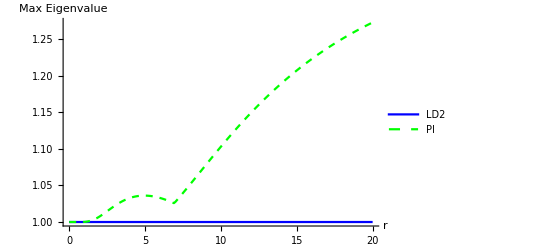

```mathematica
ListLinePlot[{Transpose[{rsLD2,maxevalsLD2}],Transpose[{rsPI,maxevalsPI}]},PlotStyle->{Blue, {Green, Dashed}}, PlotLegends->{"LD2", "PI"}, AxesLabel->{"r", "Max Eigenvalue"}]
```

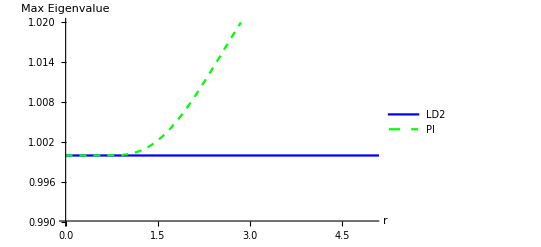

```mathematica
ListLinePlot[{Transpose[{rsLD2,maxevalsLD2}],Transpose[{rsPI,maxevalsPI}]},PlotStyle->{Blue, {Green, Dashed}}, PlotLegends->{"LD2", "PI"},PlotRange->{{0,5},{.99,1.02}}, AxesLabel->{"r", "Max Eigenvalue"}]
```

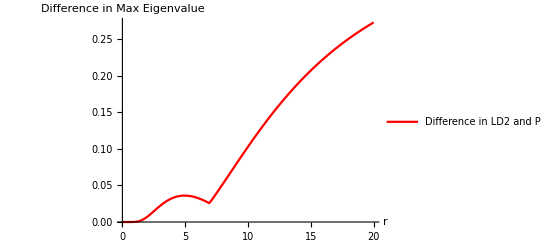

```mathematica
ListLinePlot[{Transpose[{rsLD2,Abs[maxevalsLD2 - maxevalsPI]}]},PlotStyle->{Red}, PlotLegends->{"Difference in LD2 and PI"}, AxesLabel->{"r", "Difference in Max Eigenvalue"}]
```

```mathematica
Abs[maxevalsLD2 - maxevalsPI]
```

{0,1.41711×10^-9,8.21085×10^-8,7.91871×10^-7,3.51426×10^-6,9.8075×10^-6,0.0000204288,0.0000334396,0.000042301,0.0000624937,0.000173592,0.000363602,0.000653058,0.00105875,0.00159242,0.00226022,0.00306282,0.00399598,0.00505131,0.00621728,0.00748004,0.00882431,0.0102341,0.0116933,0.0131863,0.0146979,0.0162141,0.0177219,0.0192097,0.0206669,0.0220843,0.0234539,0.0247688,0.0260232,0.0272123,0.0283322,0.0293798,0.0303528,0.0312495,0.0320687,0.03281,0.0334732,0.0340584,0.0345664,0.0349978,0.0353539,0.0356359,0.0358454,0.0359838,0.0360529,0.0360545,0.0359905,0.0358627,0.0356731,0.0354237,0.0351165,0.0347533,0.0343363,0.0338672,0.0333481,0.0327808,0.0321672,0.0315092,0.0308084,0.0300668,0.0292859,0.0284676,0.0276133,0.0267247,0.0258034,0.0275012,0.0298819,0.0322872,0.0347148,0.0371629,0.0396294,0.0421124,0.04461,0.0471206,0.0496425,0.052174,0.0547136,0.0572599,0.0598113,0.0623666,0.0649245,0.0674838,0.0700431,0.0726016,0.075158,0.0777113,0.0802607,0.0828051,0.0853437,0.0878757,0.0904002,0.0929167,0.0954242,0.0979223,0.10041,0.102887,0.105353,0.107807,0.110249,0.112678,0.115093,0.117495,0.119884,0.122257,0.124616,0.12696,0.129289,0.131602,0.1339,0.136181,0.138446,0.140695,0.142928,0.145143,0.147342,0.149524,0.151689,0.153837,0.155967,0.15808,0.160176,0.162255,0.164316,0.166359,0.168385,0.170394,0.172385,0.174359,0.176316,0.178255,0.180177,0.182081,0.183969,0.185839,0.187692,0.189527,0.191346,0.193148,0.194934,0.196702,0.198454,0.200189,0.201908,0.20361,0.205297,0.206967,0.208621,0.210259,0.211881,0.213487,0.215078,0.216654,0.218214,0.219759,0.221288,0.222803,0.224303,0.225788,0.227258,0.228714,0.230156,0.231583,0.232997,0.234396,0.235781,0.237153,0.238511,0.239856,0.241187,0.242505,0.24381,0.245102,0.246381,0.247647,0.248901,0.250143,0.251372,0.252589,0.253793,0.254986,0.256167,0.257336,0.258494,0.25964,0.260775,0.261899,0.263011,0.264112,0.265203,0.266283,0.267352,0.268411,0.269459,0.270497,0.271524,0.272542}

```mathematica
MPtest[[1,1]]//MatrixForm
```

-0.699506-0.296422 ⅈ

```mathematica
MP//MatrixForm
```

((-1024 ⅈ+r (1792+r (768 ⅈ+r (112+(100 ⅈ-9 r) r))))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r (-4 ⅈ+r) (64 ⅈ+r (-96+r (-36 ⅈ+r))))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r^2 (64 ⅈ+r (-4 ⅈ+r) (-20 ⅈ+r)))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r^3 (-16+r (-12 ⅈ+r)))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r^4 (-4 ⅈ+r))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r^5)/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (2 r^5)/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r^4 (-4 ⅈ+r))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r^3 (-16+r (-12 ⅈ+r)))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r^2 (64 ⅈ+r (-4 ⅈ+r) (-20 ⅈ+r)))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r)))
(2 r (-4 ⅈ+r) (64 ⅈ+r (-96+r (-36 ⅈ+r))))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (-1024 ⅈ+r (1792+r (768 ⅈ+r (112+(100 ⅈ-9 r) r))))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r (-4 ⅈ+r) (64 ⅈ+r (-96+r (-36 ⅈ+r))))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r^2 (64 ⅈ+r (-4 ⅈ+r) (-20 ⅈ+r)))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r^3 (-16+r (-12 ⅈ+r)))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r^4 (-4 ⅈ+r))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r^5)/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (2 r^5)/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r^4 (-4 ⅈ+r))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r^3 (-16+r (-12 ⅈ+r)))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r)))
(2 r^2 (64 ⅈ+r (-4 ⅈ+r) (-20 ⅈ+r)))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r (-4 ⅈ+r) (64 ⅈ+r (-96+r (-36 ⅈ+r))))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (-1024 ⅈ+r (1792+r (768 ⅈ+r (112+(100 ⅈ-9 r) r))))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r (-4 ⅈ+r) (64 ⅈ+r (-96+r (-36 ⅈ+r))))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r^2 (64 ⅈ+r (-4 ⅈ+r) (-20 ⅈ+r)))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r^3 (-16+r (-12 ⅈ+r)))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r^4 (-4 ⅈ+r))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r^5)/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (2 r^5)/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r^4 (-4 ⅈ+r))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r)))
(2 r^3 (-16+r (-12 ⅈ+r)))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r^2 (64 ⅈ+r (-4 ⅈ+r) (-20 ⅈ+r)))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r (-4 ⅈ+r) (64 ⅈ+r (-96+r (-36 ⅈ+r))))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (-1024 ⅈ+r (1792+r (768 ⅈ+r (112+(100 ⅈ-9 r) r))))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r (-4 ⅈ+r) (64 ⅈ+r (-96+r (-36 ⅈ+r))))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r^2 (64 ⅈ+r (-4 ⅈ+r) (-20 ⅈ+r)))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r^3 (-16+r (-12 ⅈ+r)))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r^4 (-4 ⅈ+r))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r^5)/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (2 r^5)/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r)))
(2 r^4 (-4 ⅈ+r))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r^3 (-16+r (-12 ⅈ+r)))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r^2 (64 ⅈ+r (-4 ⅈ+r) (-20 ⅈ+r)))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r (-4 ⅈ+r) (64 ⅈ+r (-96+r (-36 ⅈ+r))))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (-1024 ⅈ+r (1792+r (768 ⅈ+r (112+(100 ⅈ-9 r) r))))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r (-4 ⅈ+r) (64 ⅈ+r (-96+r (-36 ⅈ+r))))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r^2 (64 ⅈ+r (-4 ⅈ+r) (-20 ⅈ+r)))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r^3 (-16+r (-12 ⅈ+r)))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r^4 (-4 ⅈ+r))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r^5)/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
(2 r^5)/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r^4 (-4 ⅈ+r))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r^3 (-16+r (-12 ⅈ+r)))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r^2 (64 ⅈ+r (-4 ⅈ+r) (-20 ⅈ+r)))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r (-4 ⅈ+r) (64 ⅈ+r (-96+r (-36 ⅈ+r))))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (-1024 ⅈ+r (1792+r (768 ⅈ+r (112+(100 ⅈ-9 r) r))))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r (-4 ⅈ+r) (64 ⅈ+r (-96+r (-36 ⅈ+r))))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r^2 (64 ⅈ+r (-4 ⅈ+r) (-20 ⅈ+r)))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r^3 (-16+r (-12 ⅈ+r)))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r^4 (-4 ⅈ+r))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r^5)/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | (2 r^5)/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r^4 (-4 ⅈ+r))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r^3 (-16+r (-12 ⅈ+r)))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r^2 (64 ⅈ+r (-4 ⅈ+r) (-20 ⅈ+r)))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r (-4 ⅈ+r) (64 ⅈ+r (-96+r (-36 ⅈ+r))))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (-1024 ⅈ+r (1792+r (768 ⅈ+r (112+(100 ⅈ-9 r) r))))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r (-4 ⅈ+r) (64 ⅈ+r (-96+r (-36 ⅈ+r))))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r^2 (64 ⅈ+r (-4 ⅈ+r) (-20 ⅈ+r)))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r^3 (-16+r (-12 ⅈ+r)))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r^4 (-4 ⅈ+r))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r^5)/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | (2 r^5)/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r^4 (-4 ⅈ+r))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r^3 (-16+r (-12 ⅈ+r)))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r^2 (64 ⅈ+r (-4 ⅈ+r) (-20 ⅈ+r)))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r (-4 ⅈ+r) (64 ⅈ+r (-96+r (-36 ⅈ+r))))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (-1024 ⅈ+r (1792+r (768 ⅈ+r (112+(100 ⅈ-9 r) r))))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r (-4 ⅈ+r) (64 ⅈ+r (-96+r (-36 ⅈ+r))))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r^2 (64 ⅈ+r (-4 ⅈ+r) (-20 ⅈ+r)))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r^3 (-16+r (-12 ⅈ+r)))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r^4 (-4 ⅈ+r))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r^5)/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | (2 r^5)/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r^4 (-4 ⅈ+r))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r^3 (-16+r (-12 ⅈ+r)))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r^2 (64 ⅈ+r (-4 ⅈ+r) (-20 ⅈ+r)))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r (-4 ⅈ+r) (64 ⅈ+r (-96+r (-36 ⅈ+r))))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (-1024 ⅈ+r (1792+r (768 ⅈ+r (112+(100 ⅈ-9 r) r))))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r (-4 ⅈ+r) (64 ⅈ+r (-96+r (-36 ⅈ+r))))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r^2 (64 ⅈ+r (-4 ⅈ+r) (-20 ⅈ+r)))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r^3 (-16+r (-12 ⅈ+r)))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r^4 (-4 ⅈ+r))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r^5)/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | (2 r^5)/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r^4 (-4 ⅈ+r))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r^3 (-16+r (-12 ⅈ+r)))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r^2 (64 ⅈ+r (-4 ⅈ+r) (-20 ⅈ+r)))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r (-4 ⅈ+r) (64 ⅈ+r (-96+r (-36 ⅈ+r))))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (-1024 ⅈ+r (1792+r (768 ⅈ+r (112+(100 ⅈ-9 r) r))))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r (-4 ⅈ+r) (64 ⅈ+r (-96+r (-36 ⅈ+r))))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r^2 (64 ⅈ+r (-4 ⅈ+r) (-20 ⅈ+r)))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r^3 (-16+r (-12 ⅈ+r)))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r^4 (-4 ⅈ+r))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r^5)/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | (2 r^5)/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r^4 (-4 ⅈ+r))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r^3 (-16+r (-12 ⅈ+r)))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r^2 (64 ⅈ+r (-4 ⅈ+r) (-20 ⅈ+r)))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r (-4 ⅈ+r) (64 ⅈ+r (-96+r (-36 ⅈ+r))))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (-1024 ⅈ+r (1792+r (768 ⅈ+r (112+(100 ⅈ-9 r) r))))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r (-4 ⅈ+r) (64 ⅈ+r (-96+r (-36 ⅈ+r))))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r^2 (64 ⅈ+r (-4 ⅈ+r) (-20 ⅈ+r)))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r^3 (-16+r (-12 ⅈ+r)))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r^4 (-4 ⅈ+r))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r^5)/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | (2 r^5)/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r^4 (-4 ⅈ+r))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r^3 (-16+r (-12 ⅈ+r)))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r^2 (64 ⅈ+r (-4 ⅈ+r) (-20 ⅈ+r)))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r (-4 ⅈ+r) (64 ⅈ+r (-96+r (-36 ⅈ+r))))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (-1024 ⅈ+r (1792+r (768 ⅈ+r (112+(100 ⅈ-9 r) r))))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r (-4 ⅈ+r) (64 ⅈ+r (-96+r (-36 ⅈ+r))))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r^2 (64 ⅈ+r (-4 ⅈ+r) (-20 ⅈ+r)))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r^3 (-16+r (-12 ⅈ+r)))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r^4 (-4 ⅈ+r))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r^5)/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | (2 r^5)/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r^4 (-4 ⅈ+r))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r^3 (-16+r (-12 ⅈ+r)))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r^2 (64 ⅈ+r (-4 ⅈ+r) (-20 ⅈ+r)))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r (-4 ⅈ+r) (64 ⅈ+r (-96+r (-36 ⅈ+r))))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (-1024 ⅈ+r (1792+r (768 ⅈ+r (112+(100 ⅈ-9 r) r))))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r (-4 ⅈ+r) (64 ⅈ+r (-96+r (-36 ⅈ+r))))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r^2 (64 ⅈ+r (-4 ⅈ+r) (-20 ⅈ+r)))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r^3 (-16+r (-12 ⅈ+r)))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r^4 (-4 ⅈ+r))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r^5)/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (2 r^5)/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r^4 (-4 ⅈ+r))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r^3 (-16+r (-12 ⅈ+r)))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r^2 (64 ⅈ+r (-4 ⅈ+r) (-20 ⅈ+r)))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r (-4 ⅈ+r) (64 ⅈ+r (-96+r (-36 ⅈ+r))))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (-1024 ⅈ+r (1792+r (768 ⅈ+r (112+(100 ⅈ-9 r) r))))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r (-4 ⅈ+r) (64 ⅈ+r (-96+r (-36 ⅈ+r))))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r^2 (64 ⅈ+r (-4 ⅈ+r) (-20 ⅈ+r)))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r^3 (-16+r (-12 ⅈ+r)))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r^4 (-4 ⅈ+r))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r^5)/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (2 r^5)/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r^4 (-4 ⅈ+r))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r^3 (-16+r (-12 ⅈ+r)))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r^2 (64 ⅈ+r (-4 ⅈ+r) (-20 ⅈ+r)))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r (-4 ⅈ+r) (64 ⅈ+r (-96+r (-36 ⅈ+r))))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (-1024 ⅈ+r (1792+r (768 ⅈ+r (112+(100 ⅈ-9 r) r))))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r (-4 ⅈ+r) (64 ⅈ+r (-96+r (-36 ⅈ+r))))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r^2 (64 ⅈ+r (-4 ⅈ+r) (-20 ⅈ+r)))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r^3 (-16+r (-12 ⅈ+r)))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r^4 (-4 ⅈ+r))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r^5)/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r)))
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (2 r^5)/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r^4 (-4 ⅈ+r))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r^3 (-16+r (-12 ⅈ+r)))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r^2 (64 ⅈ+r (-4 ⅈ+r) (-20 ⅈ+r)))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r (-4 ⅈ+r) (64 ⅈ+r (-96+r (-36 ⅈ+r))))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (-1024 ⅈ+r (1792+r (768 ⅈ+r (112+(100 ⅈ-9 r) r))))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r (-4 ⅈ+r) (64 ⅈ+r (-96+r (-36 ⅈ+r))))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r^2 (64 ⅈ+r (-4 ⅈ+r) (-20 ⅈ+r)))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r^3 (-16+r (-12 ⅈ+r)))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r^4 (-4 ⅈ+r))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r)))
(2 r^5)/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (2 r^5)/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r^4 (-4 ⅈ+r))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r^3 (-16+r (-12 ⅈ+r)))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r^2 (64 ⅈ+r (-4 ⅈ+r) (-20 ⅈ+r)))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r (-4 ⅈ+r) (64 ⅈ+r (-96+r (-36 ⅈ+r))))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (-1024 ⅈ+r (1792+r (768 ⅈ+r (112+(100 ⅈ-9 r) r))))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r (-4 ⅈ+r) (64 ⅈ+r (-96+r (-36 ⅈ+r))))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r^2 (64 ⅈ+r (-4 ⅈ+r) (-20 ⅈ+r)))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r^3 (-16+r (-12 ⅈ+r)))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r)))
(2 r^4 (-4 ⅈ+r))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r^5)/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (2 r^5)/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r^4 (-4 ⅈ+r))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r^3 (-16+r (-12 ⅈ+r)))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r^2 (64 ⅈ+r (-4 ⅈ+r) (-20 ⅈ+r)))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r (-4 ⅈ+r) (64 ⅈ+r (-96+r (-36 ⅈ+r))))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (-1024 ⅈ+r (1792+r (768 ⅈ+r (112+(100 ⅈ-9 r) r))))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r (-4 ⅈ+r) (64 ⅈ+r (-96+r (-36 ⅈ+r))))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r^2 (64 ⅈ+r (-4 ⅈ+r) (-20 ⅈ+r)))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r)))
(2 r^3 (-16+r (-12 ⅈ+r)))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r^4 (-4 ⅈ+r))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r^5)/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (2 r^5)/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r^4 (-4 ⅈ+r))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r^3 (-16+r (-12 ⅈ+r)))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r^2 (64 ⅈ+r (-4 ⅈ+r) (-20 ⅈ+r)))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r (-4 ⅈ+r) (64 ⅈ+r (-96+r (-36 ⅈ+r))))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (-1024 ⅈ+r (1792+r (768 ⅈ+r (112+(100 ⅈ-9 r) r))))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r (-4 ⅈ+r) (64 ⅈ+r (-96+r (-36 ⅈ+r))))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r)))
(2 r^2 (64 ⅈ+r (-4 ⅈ+r) (-20 ⅈ+r)))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r^3 (-16+r (-12 ⅈ+r)))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r^4 (-4 ⅈ+r))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r^5)/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (2 r^5)/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r^4 (-4 ⅈ+r))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r^3 (-16+r (-12 ⅈ+r)))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r^2 (64 ⅈ+r (-4 ⅈ+r) (-20 ⅈ+r)))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (2 r (-4 ⅈ+r) (64 ⅈ+r (-96+r (-36 ⅈ+r))))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))) | (-1024 ⅈ+r (1792+r (768 ⅈ+r (112+(100 ⅈ-9 r) r))))/(-1024 ⅈ+11 r (-4 ⅈ+r) (64 ⅈ+r (-4 ⅈ+r) (-12 ⅈ+r))))